Adjacency list (i -> {{j, weight}, ...}):

1→{{1,1}}
2→{{1,0.25},{2,0.5},{3,0.25}}
3→{{2,0.2},{3,0.4},{4,0.2},{6,0.2}}
4→{{4,0.1667},{5,0.333},{6,0.5}}
5→{{4,0.5},{6,0.5}}
6→{{4,0.25},{6,0.75}}

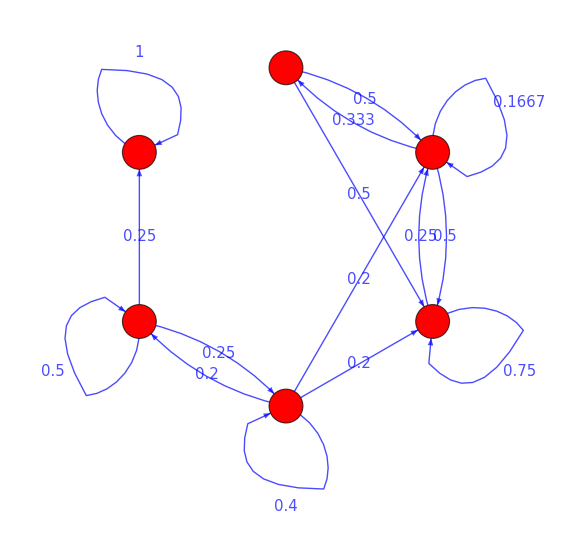

D:\Daneshgah\narm\graph.png

```mathematica
(*---1) Define your 6x6 transition matrix P---*)P={{1,0,0,0,0,0},{0.25,0.5,0.25,0,0,0},{0,0.2,0.4,0.2,0,0.2},{0,0,0,0.1667,0.333,0.5},{0,0,0,0.5,0,0.5},{0,0,0,0.25,0,0.75}};
n=Length[P];

(*---2) Build adjacency list (i->{{j,weight},...}) with only P[[i,j]]>0---*)
adjList=Table[i->Select[Table[{j,P[[i,j]]},{j,1,n}],#[[2]]>0&],{i,1,n}];
Print["Adjacency list (i -> {{j, weight}, ...}):"];
Column[adjList]

(*---3) Extract a flat list of edges and weights,adjusting indices to 0-based---*)
edgesWithWeights=Flatten[Table[If[P[[i,j]]>0,{DirectedEdge[i-1,j-1],P[[i,j]]},Nothing],{i,1,n},{j,1,n}],1];

edges=edgesWithWeights[[All,1]];
weights=edgesWithWeights[[All,2]];

(*---4) Create the graph with explicit vertex labels 0 to 5---*)
g=Graph[edges,EdgeWeight->weights,DirectedEdges->True,VertexLabels->Table[i->Placed[i,Center],{i,0,n-1}],EdgeLabels->Placed["EdgeWeight",Center],GraphLayout->"CircularEmbedding",ImagePadding->20,EdgeStyle->{Thick,Blue},VertexStyle->Red,VertexSize->Medium,BaseStyle->{FontSize->15}];

(*---5) Display and export the graph---*)
e=Show[g,PlotTheme->"Detailed",ImageSize->Large]
Export["D:\\Daneshgah\\narm\\graph.png",e]
```